```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
<<"../orientedGraphTools.m"
```

/home/armin/my_programs/alphaLoopMisc/graph_generation/example_yamlExport

The documented functions in this package are: 
 ?plotGraph 
 ?findIsomorphicGraphs 
 ?constructCuts 
 ?importGraphs 
 ?getLoopLines 
 ?getCutStructure 
 ?writeMinimalJSON 
 ?contractLorentz 
 ?contractColor 
 ?extractTensCoeff 
 ?getSymCoeff 
 ?processNumerator
 ----------------------------------------- 
 Needs the package IGraphM which can be downloaded from https://github.com/szhorvat/IGraphM. !!! 
 Run: Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"] for installation.
 Make sure you have the "trace_form.log" file for the gamma-algebra

```mathematica
(* get ben's box *)
allGraphs={importGraphs["./phi3graphs.qgr"][[-2]]};
(*kinematics=<|mass[phi]->125,
Thread@Rule[{p1,p2,p3,p4},{1,1,-1,-1}*SetPrecision[ImportString["[[6.0,0.0,0.0,5.91607978309962],
[6.0,0.0,0.0,-5.91607978309962],
[-6.0,-1.3124738333059,-5.26330888118183,2.36114210884473],
[-6.0,1.3124738333059,5.26330888118183,-2.36114210884473]]","PythonExpression"],32]]
|>;
*)
```

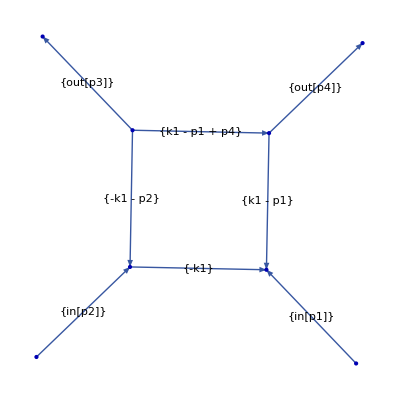

```mathematica
plotGraph[allGraphs,edgeLabels->"momentumMap"]
```

```mathematica
allGraphs[[1,"numerator"]]=SP[k1,p1];
```

```mathematica
allGraphs=getSymCoeff[allGraphs];
```

Final check started

Final check passed

```mathematica
allGraphs
```

<|edges→{in[1]→v[1],in[2]→v[2],v[4]→out[1],v[3]→out[2],v[2]→v[1],v[3]→v[1],v[4]→v[2],v[4]→v[3]},particleType→{in[phi[p1]],in[phi[p2]],out[phi[p3]],out[phi[p4]],phi,phi,phi,phi},momentumMap→{in[p1],in[p2],out[p3],out[p4],-k1,k1-p1,-k1-p2,k1-p1+p4},numerator→SP[k1,p1],loopMomenta→{k1},symmetrizedExpandedTensorCoeff→{0,vector[p1,0],vector[p1,1],vector[p1,2],vector[p1,3]}|>

```mathematica
plotGraph[allGraphs,edgeLabels->"momentumMap"]
```

-Graphics-

```mathematica
getCutStructure[allGraphs]
```

<|edges→{in[1]→v[1],in[2]→v[2],v[4]→out[1],v[3]→out[2],v[2]→v[1],v[3]→v[1],v[4]→v[2],v[4]→v[3]},particleType→{in[phi[p1]],in[phi[p2]],out[phi[p3]],out[phi[p4]],phi,phi,phi,phi},momentumMap→{in[p1],in[p2],out[p3],out[p4],-k1,k1-p1,-k1-p2,k1-p1+p4},numerator→SP[k1,p1],loopMomenta→{k1},symmetrizedExpandedTensorCoeff→{0,vector[p1,0],vector[p1,1],vector[p1,2],vector[p1,3]},loopLines→{<|signature→{1},propagators→{<|mass→mass[phi],name→prop5,power→1,q→{0,0,0,0}|>,<|mass→mass[phi],name→prop6,power→1,q→-p1|>,<|mass→mass[phi],name→prop7,power→1,q→p2|>,<|mass→mass[phi],name→prop8,power→1,q→-p1+p4|>}|>},cutStructure→{{-1}}|>

```mathematica
pp1=SetPrecision[{14,-66/10,-40,0},32];
pp3=SetPrecision[{-43,12,33,0},32];
pp4=SetPrecision[{-28,-50,10,0},32];
pp2=-pp1-pp3-pp4;
kinematics=<|mass[phi]->0,
Thread@Rule[{p1,p2,p3,p4},{1,1,-1,-1}*{pp1,pp2,pp3,pp4}]
|>;
```

```mathematica
pp4[[1]]*pp4[[1]]-pp4[[2;;]].pp4[[2;;]]
```

-1816.

```mathematica
writeMinimalJSON[allGraphs,kinematics,exportDirectory->"./tmp/",processName->"box_Lin_Test",writeNumerator->True]
Print["done"]
```

{<|external_kinematics→{{14.,-6.6,-40.,0},{57.,44.6,-3.,0},{-43.,12.,33.,0},{-28.,-50.,10.,0}},loop_lines→{<|end_node→69,propagators→{<|m_squared→0,name→prop5,power→1,q→{0.,0.,0.,0.}|>,<|m_squared→0,name→prop6,power→1,q→{-14.,6.6,40.,0.}|>,<|m_squared→0,name→prop7,power→1,q→{57.,44.6,-3.,0.}|>,<|m_squared→0,name→prop8,power→1,q→{14.,56.6,30.,0.}|>},signature→{1},start_node→70|>},ltd_cut_structure→{{-1}},maximum_ratio_expansion_threshold→-1,n_loops→1,numerator_tensor_coefficients→{{0.,0.},{14.,0.},{6.6,0.},{40.,0.},{0.,0.}},name→box_Lin_Testdiag_1|>}

done

```mathematica
allGraphs[["momentumMap"]]
```

{in[p1],in[p2],out[p3],out[p4],-k1,k1-p1,-k1-p2,k1-p1+p4}

```mathematica
getLoopLines[allGraphs]
```

<|edges→{in[1]→v[1],in[2]→v[2],v[4]→out[1],v[3]→out[2],v[2]→v[1],v[3]→v[1],v[4]→v[2],v[4]→v[3]},particleType→{in[phi[p1]],in[phi[p2]],out[phi[p3]],out[phi[p4]],phi,phi,phi,phi},momentumMap→{in[p1],in[p2],out[p3],out[p4],-k1,k1-p1,-k1-p2,k1-p1+p4},numerator→SP[k1,p1],loopMomenta→{k1},symmetrizedExpandedTensorCoeff→{0,vector[p1,0],vector[p1,1],vector[p1,2],vector[p1,3]},loopLines→{<|signature→{1},propagators→{<|mass→mass[phi],name→prop5,power→1,q→{0,0,0,0}|>,<|mass→mass[phi],name→prop6,power→1,q→-p1|>,<|mass→mass[phi],name→prop7,power→1,q→p2|>,<|mass→mass[phi],name→prop8,power→1,q→-p1+p4|>}|>}|>

```mathematica
"--14.0
--6.6
--40.0
-0.0
--57.0
-44.6
--3.0
--0.0
---43.0
-12.0
-33.0
-0.0
---28.0
--50.0
-10.0
-0.0"
```